### Definition

```mathematica
a=1;
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-α/r+Ff E^(-Fg r);
```

```mathematica
(*RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@1/(m α);*)
```

```mathematica
{Ff,Fg}={-4.20415644616125582469299138439140113373493210258692526366760104908016252690683`50.,1.88979567639491639010430213789778028047296373449456361136288297937037496900499`50.};
```

```mathematica
(*RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]*)
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=Table[
PrintTemporary[n];e/.FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[evShifted],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])(*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
PrintTemporary[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]];
δexpminus9=δ50e[10^-9,V[r]];
δexpminus5=δ50e[10^-5,V[r]];
(*δ50V=δ50[V[r]]*)
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031979700136220568923737045153765763046169357856) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867631708196101944706820810514600259947125) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095933881080621951847950360718656142026828058) is less than WorkingPrecision (50.).

```mathematica
(*Get["C:\\Users\\ASUS\\Documents\\Coulombshortrange_psir_comparasion2.mx"]*)
```

```mathematica
energyV=EigenEnergy[V[r],αSch,{10^-15,Which[n<10,1200,11≤n<15,2000,15≤n<19,4000,n≥19,6000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.3822,-0.182736,-0.0703652,-0.0371487,-0.0229267,-0.0155492,-0.0112354,-0.00849649,-0.00664955,-0.00534542,-0.00439048,-0.00367033,-0.00311387,-0.00267499,-0.00232276,-0.00203579,-0.00179889,-0.00160106,-0.00143415,-0.00129204}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.38219883569251964490160550178,-0.182735548644294965391472479982,-0.0703651929305044526873468208911,-0.0371486908262772367228809683984,-0.0229266892452571839793215565183,-0.015549231855268271662743862639,-0.0112354034510922371458303980945,-0.00849649089104768482214222423255,-0.00664954945575757032547258191275,-0.00534541930999999288840343990216,-0.00439047850565455340950424438103,-0.00367033275768893493625065023157,-0.00311386894651937123211165611551,-0.00267499298242404164149687581397,-0.00232276446482711850577060037957,-0.00203578876875274255140779242833,-0.00179888914714337109743248601297,-0.00160105779102435795711572789934,-0.00143415380651512489019984377974,-0.00129206404614123306285529128761}

```mathematica
(*efV=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V[r],energyV[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-5];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
];*)
```

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-1.38219883569251964490160550178 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0371486908262772367228809683984 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0112354034510922371458303980945 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00534541930999999288840343990216 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00439047850565455340950424438103 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0229266892452571839793215565183 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00849649089104768482214222423255 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.182735548644294965391472479982 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00367033275768893493625065023157 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.015549231855268271662743862639 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00664954945575757032547258191275 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.0703651929305044526873468208911 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00311386894651937123211165611551 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00232276446482711850577060037957 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00179888914714337109743248601297 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00143415380651512489019984377974 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00267499298242404164149687581397 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00203578876875274255140779242833 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00160105779102435795711572789934 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) f[r]-f''[r]/2==-0.00129206404614123306285529128761 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{9.16469666377×10^-1396                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-8.76787738327×10^-472                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],7.259×10^-270                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.20942×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.96817×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.47749×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.29983×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.39821×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.90856×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.088×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.79526×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.000015697                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],90.5726                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.08148×10^7                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],7.18103×10^12                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.3503×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],2.21405×10^-26                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-1.41913×10^-19                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],1.87333×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-6.37992×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}

```mathematica
<<C:\\Users\\ASUS\\Documents\\Coulombshortrange_psir_comparasion_efV.mx
<<C:\\Users\\ASUS\\Documents\\Coulombshortrange_psir_comparasion_efVs2.mx
```

### Determine c_1

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end___},opt___]:=Module[{aaa,findroot,mon},aaa=a;
Print[aaa];
Monitor[findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>{mon={c1,evnhhhc1[c1]}}],mon];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},{MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50}]
```

#### Vs_1’s eigensystem

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{10^-15,Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
N[%,6]
```

```mathematica
efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
];
```

#### ψ_r Vs_1

```mathematica
IntegrationVs11st=NIntegrate[efVs1[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20;
```

```mathematica
ψrTrueVs1[n_][γ_,η_]:=4π(γ Integration1st[[n]])
```

```mathematica
DetermineVs1[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[n,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs1[#][γ,η]&/@REFRANGE==REF],{γ,0,1},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{r0,γ}(*,N[ERROR,6]*)/.RES
]
```

```mathematica
Determine[0]
```

```mathematica
Module[{γη},
γlVs1={};
Monitor[Table[
γη=Determine[r0];
AppendTo[γlVs1,γη];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
γrVs1=Interpolation[γlVs1]
```

```mathematica
ψrfunVs1[r_][n_]:=4π(γrVs1[r] IntegrationVs11st[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs1[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs1[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

### Determine c_2 & d_1

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[10^-9,c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1[{c2start_,c2end___},{d1start_,d1end___}]:=Module[{findroot,mon},
Monitor[findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[10^-9,c2,d1]==δexpminus9},{{c2,c2start,c2end},{d1,d1start,d1end}},MaxIterations->100,PrecisionGoal->20,WorkingPrecision->30,StepMonitor:>{mon={c2,d1,evnhhh1,evnhhh2}}],mon];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1[{-40},{3}]
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-36.2721977586520215810233663642,5.44392496851752441595698657669}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Coulombshortrange_psir_comparasion.mx",{c2,d1}];
DumpSave["C:\\Users\\ASUS\\Documents\\Coulombshortrange_psir_comparasion_efV.mx",efV];
DumpSave["C:\\Users\\ASUS\\Documents\\Coulombshortrange_psir_comparasion_efVs2.mx",efVs2];
```

#### Vs_2’s eigensystem

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{10^-15,Which[n<10,1200,11≤n<15,2000,15≤n<19,4000,n≥19,6000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.59768,-0.180602,-0.0702185,-0.0371215,-0.0229188,-0.0155463,-0.0112341,-0.00849586,-0.00664921,-0.00534522,-0.00439036,-0.00367026,-0.00311382,-0.00267496,-0.00232274,-0.00203577,-0.00179888,-0.00160105,-0.00143415,-0.00129203}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.59768493239021798316997312929,-0.180602285051875695894278489152,-0.0702185117971132268034536442755,-0.0371214599143007575452100816997,-0.022918840661015098313769511633,-0.0155463160955231876441832477273,-0.0112341240725214596088178412758,-0.0084958592354953569706604735691,-0.00664920885965450038224764235853,-0.00534522265055336368882782400535,-0.0043903585716162386897194343606,-0.00367025626873855314258410839297,-0.00311381831204068704762514797477,-0.00267495838866846729912037587044,-0.0023227401820021952615340116989,-0.00203577131904180063608995430967,-0.00179887634759828034699271974568,-0.00160104823269717477796092452991,-0.00143414660231775461984887805968,-0.00129207204509249472934364235838}

```mathematica
(energyVs2-energyV)/energyV
```

{0.155900939237684913247419497,-0.0116740481435923953479469956,-0.00208456947650373360837729109,-0.00073302480843328430987239026,-0.00034233395664440702122048515,-0.0001875179283596651221314996,-0.0001138702830162421679339213,-0.00007434310945868186934994106,-0.00005122092937816036873125762,-0.00003679027504190309015318206,-0.00002731684898588051467283058,-0.00002083978631680135962239019,-0.0000162609536733338856976773,-0.0000129322790009691889666711,-0.0000104542777758792636564913,-8.57147421665271928003357×10^-6,-7.11524949220804801379097×10^-6,-5.97000760170170372958549×10^-6,-5.0233087535959302788923×10^-6,6.19083185973285584784284×10^-6}

```mathematica
efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-5];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
];
```

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371214599143007575452100816997 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112341240725214596088178412758 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534522265055336368882782400535 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.59768493239021798316997312929 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0043903585716162386897194343606 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.022918840661015098313769511633 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0084958592354953569706604735691 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.180602285051875695894278489152 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367025626873855314258410839297 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155463160955231876441832477273 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664920885965450038224764235853 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0702185117971132268034536442755 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311381831204068704762514797477 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0023227401820021952615340116989 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179887634759828034699271974568 f[r],f[4000]==«23»,f'[4000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143414660231775461984887805968 f[r],f[4000]==«23»,f'[4000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267495838866846729912037587044 f[r],f[2000]==«23»,f'[2000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203577131904180063608995430967 f[r],f[4000]==«23»,f'[4000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160104823269717477796092452991 f[r],f[4000]==«23»,f'[4000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00129207204509249472934364235838 f[r],f[4000]==«23»,f'[4000]==-1.×10^-50},«3»,{}}) is less than WorkingPrecision (50.).

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

NIntegrate::precw: The precision of the argument function (3.1938326062×10^-1506 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},«31»,{41},{42},{43},{44},{45},{46},{47},{48},{49},«60478»},{«1»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-1.97754199053×10^-470 ⅇ^(-r^2/2) r InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (2.8699×10^-271 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},«23»,{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«14411»},{«1»}}}][r]) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{0.0117776206955657427963565426932,-0.000395709850941589426621166036455,-0.000228014646081170321415317850449,-0.000146454016141419798635699581955,-0.000103434947974171163961195973272,-0.000077850611626185712079289830881,-0.0000612599647704786549085356701444,-0.0000498040121809601651355470873945,-0.0000415110539895395549215108143775,-0.0000352835129776020802581255343755,-0.0000304681115662695058124969244761,-0.0000266546823635176991592163195616,-0.0000235742384515362210671336506023,-0.0000210438898537119713385792620538,-0.0000189354417417103748488341623142,-0.0000171566706922855954596613648305,-0.0000156397238082449353590221778211,-0.000014333694122932146395121765061,-0.000013200173244311877962165953481,-0.0000122402560823559615188841232704}

NIntegrate::precw: The precision of the argument function (5.03016177796×10^-1505 r«1»«1» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},«31»,{41},{42},{43},{44},{45},{46},{47},{48},{49},«60478»},{«1»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-3.11455150022×10^-469 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) InterpolatingFunction[«1»][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-0.0194412219859862127128023407616,-0.00707832358850827308539284618836,-0.00320936166211520742704863651468,-0.00193741943716303315475040791917,-0.00133383010081773269358667253866,-0.000990926051976821073144885139847,-0.000773891662246764561257462454527,-0.000626180203105176246003717650254,-0.000520246206829715670332276351772,-0.000441202543459361806978520109638,-0.000380361133203316410276446842787,-0.000332341946219510785468180402308,-0.000293652214187590233191705123109,-0.000261935133904024331188393493532,-0.000235548421159276900845442811833,-0.000213316090659724220505356235265,-0.000194376145945289692281825489677,-0.000178083797770853627644796032479,-0.000163947595734358120584364314116,-0.000151553667465266223038629118523}

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

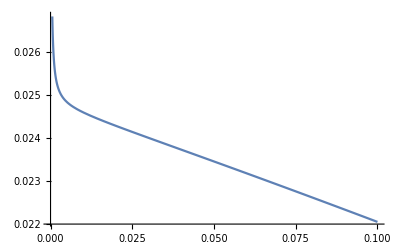

```mathematica
Plot[efV[[20]]/r,{r,0,0.1}]
```

```mathematica
NLimit[efV[[20]]/(√(4π)r),r->0,WorkingPrecision->30,Terms->7,Scale->100]
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

NLimit[-1/r 1.79974×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],r→0,WorkingPrecision→30,Terms→7,Scale→100]

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

FindRoot::precw: The precision of the argument function ({4 π (-0.0000189354417417103748488341623142 γ-0.000235548421159276900845442811833 η)==0.0107937,4 π (-0.0000122402560823559615188841232704 γ-0.000151553667465266223038629118523 η)==«6»[«1»]}) is less than WorkingPrecision (30.).

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit::noise will be suppressed during this calculation.

FindRoot::nlnum: The function value {-0.0107936825860885932115706964396,-1. NLimit[-(1.79974106361862144610485095796×10^-8 InterpolatingFunction[{{«75»,4000.}},«4»][r])/r,r→0]} is not a list of numbers with dimensions {2} at {γ,η} = {0,0}.

FindRoot::precw: The precision of the argument function ({4 π (-0.0000189354417417103748488341623142 γ-0.000235548421159276900845442811833 η)==0.0107937,4 π (-0.0000122402560823559615188841232704 γ-0.000151553667465266223038629118523 η)==«6»[«1»]}) is less than WorkingPrecision (30.).

FindRoot::nlnum: The function value {-0.0107936825860885932115706964396,-1. NLimit[-(1.79974106361862144610485095796×10^-8 InterpolatingFunction[{{«75»,4000.}},«4»][r])/r,r→0]} is not a list of numbers with dimensions {2} at {γ,η} = {0,0}.

FindRoot::precw: The precision of the argument function ({4 π (-0.0000189354417417103748488341623142 γ-0.000235548421159276900845442811833 η)==0.0107937,4 π (-0.0000122402560823559615188841232704 γ-0.000151553667465266223038629118523 η)==«6»[«1»]}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::nlnum: The function value {-0.0107936825860885932115706964396,-1. NLimit[-(1.79974106361862144610485095796×10^-8 InterpolatingFunction[{{«75»,4000.}},«4»][r])/r,r→0]} is not a list of numbers with dimensions {2} at {γ,η} = {0,0}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Thread[(ψrTrueVs2[Slot[«1»]][γ,η]&)/@REFRANGE$107962==REF$107962],{{γ,0,1},{η,0,1}},AccuracyGoal→10,MaxIterations→200,WorkingPrecision→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{0,γ},{0,η}}/.FindRoot[Thread[(ψrTrueVs2[#1][γ,η]&)/@REFRANGE$107962==REF$107962],{{γ,0,1},{η,0,1}},AccuracyGoal→10,MaxIterations→200,WorkingPrecision→30]

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=Determine[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[1]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γr[r] Integration1st[[n]]+ηr[r] a^2 Integration2nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

{-0.000503038637293077967236527899532,-9.031698599411804633997441409×10^-16}time:1.989909s

{-0.000503038637293077967236527899532}